#### BC_DirectPath_supp_1.nb This demonstrates an interesting transition along a direct path between two elastic maps. The interesting part is the shape of the beta curves for the closest-to-Sigma maps along the direct path. Requires running BC_DirectPath.nb first, using specific settings (which need to be uncommented).

```mathematica
SigCurve=TET;
```

```mathematica
Tmat1==TTET
Tmat2==TXISO
```

True

True

#### Get data from BC_DirectPath.nb

```mathematica
dt
```

0.05

#### Check the beta for the peak of the discretized curve

```mathematica
betamax =Max[βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree&/@Ranget]
```

6.64156

#### Round is necessary for Mathematica to recognize, for example, that 0.25 + 0.05 = 0.3

```mathematica
slope[t_]:=((βT[TT[Round[t+dt,.05],Tmat1,Tmat2],SigCurve]-βT[TT[t,Tmat1,Tmat2],SigCurve])/Degree)/dt;
```

#### Slope of each segment

```mathematica
MatrixNote[Tmat]
Ranget
dt
TableForm[Join[{{"   t","  βTET","  slope"}},{PaddedForm[#,{2,2}],PaddedForm[Round[βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree,.001],{4,3}],PaddedForm[slope[#],{5,2}]}&/@Ranget]]
```

T is BrownAn00

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

0.05

t |   βTET |   slope
 0.00 |  0.000 |   10.67
 0.05 |  0.534 |   10.76
 0.10 |  1.072 |   10.85
 0.15 |  1.614 |   10.93
 0.20 |  2.161 |   11.00
 0.25 |  2.711 |   11.07
 0.30 |  3.265 |   11.14
 0.35 |  3.821 |   11.19
 0.40 |  4.381 |   11.24
 0.45 |  4.943 |   11.29
 0.50 |  5.508 |   11.32
 0.55 |  6.074 |   11.35
 0.60 |  6.642 |  -10.75
 0.65 |  6.104 |  -17.35
 0.70 |  5.237 |  -17.40
 0.75 |  4.367 |  -17.43
 0.80 |  3.495 |  -17.46
 0.85 |  2.622 |  -17.48
 0.90 |  1.748 |  -17.48
 0.95 |  0.874 |  -17.48
 1.00 |  0.000 |  1980.00

#### Find the intersection between t = tt1 and t = tt2

```mathematica
tt1=.45;tt2=.65;
beta1=βT[TT[tt1,Tmat1,Tmat2],SigCurve]/Degree;
beta2=βT[TT[tt2,Tmat1,Tmat2],SigCurve]/Degree;
peak=({t,beta}/.Solve[(beta-beta1)/(t-tt1)==slope[tt1]&&(beta-beta2)/(t-tt2)==slope[tt2],{t,beta}])[[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.611711,6.76852}

T is BrownAn00

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

0.05

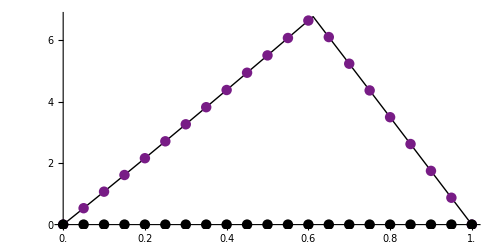

```mathematica
MatrixNote[Tmat]
Ranget
dt
plot=Graphics[{PointSize[.015],
Line[Sort[Join[{peak},{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}&/@Ranget]]],
{ColorData["Rainbow"][0/6],Point[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}]&/@Ranget},
Point[{#,0}]&/@Ranget},Axes->True,AxesOrigin->{t1,0},AspectRatio->.5,ImageSize->500,Ticks->{Range[0,1,.2],Range[0,8,2]},TicksStyle->14]
```

```mathematica
npts =10000;
AlphaMONOvalues=Sort[Table[Alpha[Tmat2,{RandomReal[{-π,π}],RandomReal[{0,π}]},MONO]/Degree,{k,npts}]];
Take[AlphaMONOvalues,5]
Take[AlphaMONOvalues,-5]
```

{0.00682068,0.0188303,0.0225377,0.0247122,0.0297483}

{15.1558,15.1558,15.1558,15.1558,15.1558}

```mathematica
cmin=0;cmax=20; dc=2;
contours=Range[cmin,cmax,dc];
MaxForScaling=cmax-dc;
eye=20xyztp[{30,65}];
```

```mathematica
(* MaxForScaling=20.5; contours=Range[0,22,2]; *)
```

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
PrintEye;
tIsPt2onBottom=Show[cpMONO[TT[.2,Tmat1,Tmat2],contours,MaxForScaling,plotpoints,contourstyle],options]
```

T is BrownAn00

{0,2,4,6,8,10,12,14,16,18,20}

18

eye = {15.7,9.06,8.45};  (θ, ϕ)_eye = {30,65}, ρ_eye = 20

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
PrintEye;
tIsPt4onBottom=Show[cpMONO[TT[.4,Tmat1,Tmat2],contours,MaxForScaling,plotpoints,contourstyle],options]
```

T is BrownAn00

{0,2,4,6,8,10,12,14,16,18,20}

18

eye = {15.7,9.06,8.45};  (θ, ϕ)_eye = {30,65}, ρ_eye = 20

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
PrintEye;
tIsPt6onBottom=Show[cpMONO[TT[.6,Tmat1,Tmat2],contours,MaxForScaling,plotpoints,contourstyle],options]
```

T is BrownAn00

{0,2,4,6,8,10,12,14,16,18,20}

18

eye = {15.7,9.06,8.45};  (θ, ϕ)_eye = {30,65}, ρ_eye = 20

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
AngRad=.05;
ShiftToEye=.02;
tkns=.01; (* tkns only affects XISO *)
PrintEye;
tIsPt2onTop=Show[{cpMONO[Closest[TT[.2,Tmat1,Tmat2],SigCurve],contours,MaxForScaling,plotpoints,contourstyle],
Graphics3D[TwoFoldGraphics[SigCurve,UT[TT[.2,Tmat1,Tmat2],SigCurve],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options]
```

T is BrownAn00

{0,2,4,6,8,10,12,14,16,18,20}

18

eye = {15.7,9.06,8.45};  (θ, ϕ)_eye = {30,65}, ρ_eye = 20

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
PrintEye;
tIsPt4onTop=Show[{cpMONO[Closest[TT[.4,Tmat1,Tmat2],SigCurve],contours,MaxForScaling,plotpoints,contourstyle],
Graphics3D[TwoFoldGraphics[SigCurve,UT[TT[.4,Tmat1,Tmat2],SigCurve],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options]
```

T is BrownAn00

{0,2,4,6,8,10,12,14,16,18,20}

18

eye = {15.7,9.06,8.45};  (θ, ϕ)_eye = {30,65}, ρ_eye = 20

#### This is what we are up against :

```mathematica
Ranget[[13]]==.6
βT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve]==βT[TT[.6,Tmat1,Tmat2],SigCurve]
```

True

False

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
PrintEye;
Ranget[[13]]
tIsPt6onTop=Show[{cpMONO[Closest[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve],contours,MaxForScaling,plotpoints,contourstyle],
Graphics3D[TwoFoldGraphics[SigCurve,UT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options]
```

T is BrownAn00

{0,2,4,6,8,10,12,14,16,18,20}

18

eye = {15.7,9.06,8.45};  (θ, ϕ)_eye = {30,65}, ρ_eye = 20

0.6

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
PrintEye;
AngRad=.05;
ShiftToEye=.02;
tIsPt8onTop=Show[{                                                         cpMONO[Closest[TT[.8,Tmat1,Tmat2],SigCurve],contours,MaxForScaling,plotpoints,contourstyle],
Graphics3D[TwoFoldGraphics[SigCurve,UT[TT[.8,Tmat1,Tmat2], SigCurve],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options]
```

T is BrownAn00

{0,2,4,6,8,10,12,14,16,18,20}

18

eye = {15.7,9.06,8.45};  (θ, ϕ)_eye = {30,65}, ρ_eye = 20

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
PrintEye;
tIs1=Show[{cpMONO[Tmat2,contours,MaxForScaling,plotpoints,contourstyle],
Graphics3D[TwoFoldGraphics[Sig2,UT[Tmat,Sig2],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options]
```

T is BrownAn00

{0,2,4,6,8,10,12,14,16,18,20}

18

eye = {15.7,9.06,8.45};  (θ, ϕ)_eye = {30,65}, ρ_eye = 20

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
PrintEye;
tIs0=Show[{cpMONO[Tmat1,contours,MaxForScaling,plotpoints,contourstyle],
Graphics3D[TwoFoldGraphics[Sig1,UT[Tmat,Sig1],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options]
```

T is BrownAn00

{0,2,4,6,8,10,12,14,16,18,20}

18

eye = {15.7,9.06,8.45};  (θ, ϕ)_eye = {30,65}, ρ_eye = 20

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
PrintEye;
tIsPt8onBottom=Show[cpMONO[TT[.8,Tmat1,Tmat2],contours,MaxForScaling,plotpoints,contourstyle],options]
```

T is BrownAn00

{0,2,4,6,8,10,12,14,16,18,20}

18

eye = {15.7,9.06,8.45};  (θ, ϕ)_eye = {30,65}, ρ_eye = 20

```mathematica
MatrixNote[Tmat]
Ranget
contours
MaxForScaling
PrintEye;
Graphics[{PointSize[.013],
{PointSize[.001],Point/@{{.1,-14.0},{.5,20.0}}},   (* fake points *)
{HueOfΣ[SigCurve],Line[Sort[Join[{peak},{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}&/@Ranget]]]},
{HueOfΣ[SigCurve],Point[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}]&/@Ranget},
Line[{{#,0},{#,-2.3}}]&/@Range[0,1,.2],
Line[{{Ranget[[#]],           βT[TT[Ranget[[#]],Tmat1,Tmat2],SigCurve]/Degree},
    {Ranget[[#]],2.4+βT[TT[Ranget[[#]],Tmat1,Tmat2],SigCurve]/Degree}}]&/@{1,5,9,13,17,21},
Text[Style["(0, 0)",18],{-.05,0}],
Text[Style["(1, 0)",18],{1.05,0}],
Inset[tIsPt2onTop,{.2,7.8+βT[TT[.2,Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIsPt4onTop,{.4,7.8+βT[TT[.4,Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIsPt6onTop,{.6,7.8+βT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIsPt8onTop,{.8,7.8+βT[TT[.8,Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIs0,{0,7.8},Center,.18],,
Inset[tIs1,{1,7.8},Center,.18],
Inset[tIsPt2onBottom,{.2,-8.0},Center,.18],
Inset[tIsPt4onBottom,{.4,-8.0},Center,.18],
Inset[tIsPt6onBottom,{.6,-8.0},Center,.18],
Inset[tIsPt8onBottom,{.8,-8.0},Center,.18],
Inset[tIs0,{0,-8.0},Center,.18],
Inset[tIs1,{1,-8.0},Center,.18],
(* TRIV base curve *)
{HueOfΣ[TRIV],Line[{{0,0},{1,0}}]},
{HueOfΣ[TRIV],Point[{#,0}]&/@Ranget}
},Axes->False,AspectRatio->.5,ImageSize->1000,PlotRange->All]
```

T is BrownAn00

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

{0,2,4,6,8,10,12,14,16,18,20}

18

eye = {15.7,9.06,8.45};  (θ, ϕ)_eye = {30,65}, ρ_eye = 20

## Brown: dt = 0.05, Tmat1=TTET, Tmat2=TXISO, ListSigma = {MONO,TET,XISO} [supp1]

#### From BC_Superlattice.nb (dt = 0.2)

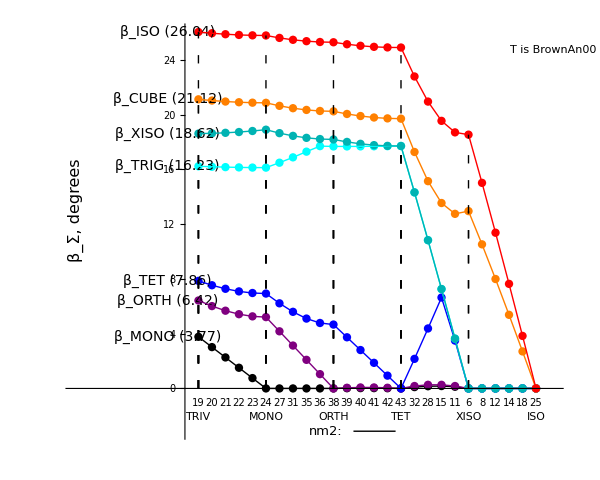

#### From BC_DirectPath.nb